```mathematica
ClearAll["Global`*"]
```

```mathematica
L=2*2.2;
h=0.41;
μ=0.001;
```

```mathematica
(*here put the latest snapshot of v generated by the dynamics*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/channel_with_cylinder_flat_cn/solution/snapshots/csv/nodal_values/v_n_128.csv"];
t=Drop[t,{1}]
```

```mathematica
For[vnum={};i=1, i<= Length[t], i++,
If[Abs[t[[i,4]]-L]<ϵ,AppendTo[vnum,{t[[i,5]],t[[i,1]]}]];
]
```

```mathematica
vnum
```

{{0.41,1.92895×10^-6},{0.328,1.14065},{0.246,1.19527},{0.164,1.19262},{0.082,1.14173},{0.,-1.09451×10^-6}}

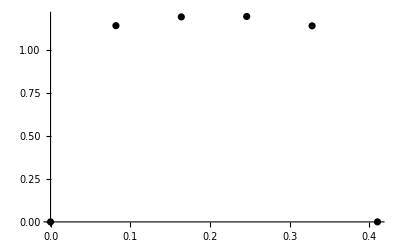

```mathematica
plotnum=ListPlot[vnum,PlotStyle->Black]
```

```mathematica
(*pick an index i0 in the middle of vnum*)
i0=Round[Length[vnum]/2];
y0=vnum[[i0,1]]
v0=vnum[[i0,2]]
```

0.246

1.19527

```mathematica
v[y_]:=Δ y*(y-h)
```

```mathematica
sol=Flatten[Solve[v[y0]==v0,Δ]]
```

{Δ→-29.6269}

```mathematica
Δ=Δ/.sol
```

-29.6269

```mathematica
v[h/2]
```

1.24507

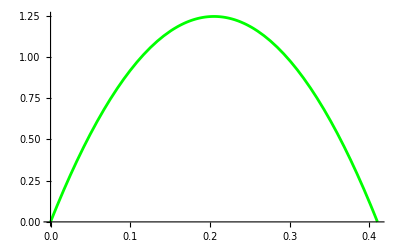

```mathematica
Show[Plot[v[y],{y,0,h}, PlotStyle->Green]]
```

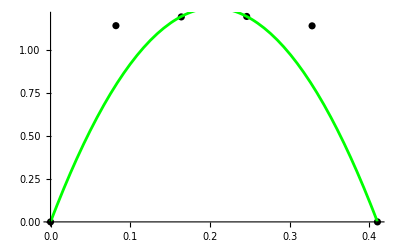

```mathematica
Show[plotnum,Plot[v[y],{y,0,h}, PlotStyle->Green]]
```